## Transformation of Love 2

Assumptions
1. Random pairs of players are chosen, and they will marriage when the following conditions are met. When the pair succeeds in getting marriage, both of agents will receive benefit v>0. If they do not succeed,  both individuals receive zero. 
   
2. Each player has a class score, s, which is known to every other player. If a player marriage other player, then their class scores will be an average of their class scores. For example when a player with score 0 got marriage other player with score 1, their class scores are (0+1)/2=0.5. 
If they fail to marriage, the class score does not change.
   
3. We consider strategies where players decide to marriage according to the class score of the partner. A strategy is given by a number x in {0, 0.2, 0.4, 0.6, 0.8, 1}. For any randomly matched players, they marriage if, and only if, the difference between class scores of the two players is smaller than their strategy x respectively. The strategy x=0 represents the players who want within class marriage, whereas the strategy x=1 represents the players who want class free marriage. At the beginning of generation, the class score are only low (score 0) and high (score 1) class. There is no middle class.
   
4. In succession, m pairs are chosen. The fitness of a player is given by the total number of points received during the m interactions. Some players may never be chosen, in which case their payoff from the game will be 0.001. On average, a player will be chosen 2 m/n times.
   
5. At the end of each generation, players leave offspring in proportion to their fitness.

## trans02

```mathematica
戦略別に適合度を計算して，各個体にルーレットセレクションを実行する
```

```mathematica
(* trans02 マッチング成功時にのみ利得増加 *)
trans02[n_(*集団人数*),m_(*1世代内のペア数*),gene_(*世代*),v_(*婚成立時の利得*)]:=Module[{id(*n人分の個体番号*),klist(*　n人分の戦略*),
k0={0,0.2,0.4,0.6,0.8,1}(*適合度計算用*),
class(*n人分の階層スコア*),benefit(*n人分の利得*),pair(*マッチングした番号*),
fit(*核戦略の適合度*)},

(*初期条件の入力 *)
id=Range[n];(* マッチング用個体番号 *)
class=Table[Random[Integer,{0,1}],{n}];(*　階層スコア初期値 Print[class];*)
klist=Table[0.2*Random[Integer,{0,5}],{n}];(*　戦略kの初期値　0--1間を0.2刻み;Print[klist];*)
benefit=Table[0,{n}];(*利得の初期値態 *)

Do[(* ここから1世代内での行動を指定する *)
(*最初に利得benefit，適合度fitを初期化する*)
benefit=Table[0,{n}];(* 利得benefit初期化 *)
fit={0,0,0,0,0,0};(*戦略別適合度fitの初期化*)

Do[(*「pairを一個だけ作る操作」をm回反復してm個のペアを作る．
classはペアを1個作るたびに1世代内(gene内)でも更新される． *)
pair=RandomSample[id,2];(*　ペアを一つ作る　*)
If[(Abs[class⟦pair⟦1⟧⟧-class⟦pair⟦2⟧⟧]≤klist⟦pair⟦1⟧⟧)&& 
(Abs[class⟦pair⟦1⟧⟧-class⟦pair⟦2⟧⟧]≤klist⟦pair⟦2⟧⟧),
(* 相手の階層スコアをチェック.お互いに許容範囲の場合，利得と階層スコアを更新する *)
benefit⟦pair⟦2⟧⟧=benefit⟦pair⟦2⟧⟧+v;benefit⟦pair⟦1⟧⟧=benefit⟦pair⟦1⟧⟧+v;
class⟦pair⟦1⟧⟧=class⟦pair⟦2⟧⟧=(class⟦pair⟦1⟧⟧+class⟦pair⟦2⟧⟧)/2.0](*If終わり*)
(* Ifおわり*),{m}];(*m個のマッチング反復終わり ;Print["class",class]; *)
benefit=benefit+0.01;(* 0要素を消す *)
(*戦略別に利得を合計して適合度fitに代入*)
Table[Table[If[klist⟦i⟧==k0⟦j⟧,fit⟦j⟧=fit⟦j⟧+benefit⟦i⟧],{j,1,6}],{i,1,n}];
(*  適合度に基づくルーレットセレクション　Print["fit",fit];  Print["klist",klist];*)

klist=Table[RandomChoice[(*weight*)fit->{0,0.2,0.4,0.6,0.8,1}],{i,1,n}],{gene}];
{ListPlot[Transpose[{Table[i,{i,0,1,0.1}],BinCounts[class,{0,1.1,0.1}]}],Filling->Axis,PlotRange->{0,n+1}],
ListPlot[Transpose[{Table[i,{i,0,1,0.2}],BinCounts[klist,{0,1.2,0.2}]}],Filling->Axis,PlotRange->{0,n+1}]}
]
```

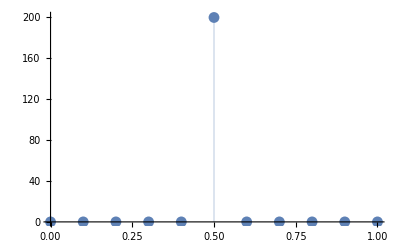
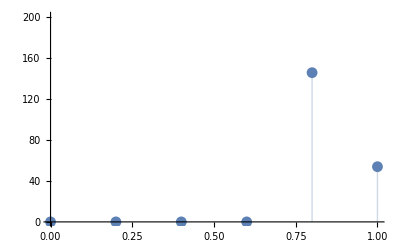

```mathematica
trans02[200(*集団人数*),100(*1世代内のペア数*),50(*世代*),2(*婚成立時の利得*)]
```

```mathematica
trans02[150(*集団人数*),50(*1世代内のペア数*),50(*世代*),2(*婚成立時の利得*)]
trans02[150(*集団人数*),50(*1世代内のペア数*),50(*世代*),2(*恋愛婚成立時の利得*)]
trans02[150(*集団人数*),50(*1世代内のペア数*),50(*世代*),2(*恋愛婚成立時の利得*)]
```

## trans03 gene別に出力

```mathematica
trans03[a_(* 戦略初期配置 *),h_(*階級初期配置*),n_(*集団人数*),m_(*1世代内のペア数*),
gene_(*世代*),v_(*婚成立時の利得*),dx_(*output 刻み*)]:=
Module[{id(*n人分の個体番号*),klist(*　n人分の戦略*),
k0={0,0.2,0.4,0.6,0.8,1}(*適合度計算用*),
class(*n人分の階層スコア*),benefit(*n人分の利得*),pair(*マッチングした番号*),
fit(*核戦略の適合度*),out1,out2,klist1,klist2,klist3},

(*初期条件の入力 *)
id=Range[n];(* マッチング用個体番号 *)
class=Table[RandomChoice[{1-h,h}->{0,1}],{n}];(*　階層スコア初期値 高階層の割合h，Print[class];*)
klist=Table[RandomChoice[{a,(1-a)/5,(1-a)/5,(1-a)/5,(1-a)/5,(1-a)/5}->{0,0.2,0.4,0.6,0.8,1.0}],{n}];
(*　戦略kの初期値　0--1間を0.2刻み;Print[klist];klist1=Table[0.2*Random[Integer,{0,5}],{n}];*)

(* Which[op==1,klist=klist1,
op==2,klist=klist2]; 戦略の初期分布をopの値で設定 *)

out1={klist};out2={class};
benefit=Table[0,{n}];(*利得の初期値態 *)

Do[(* ここから1世代内での行動を指定する *)
(*最初に利得benefit，適合度fitを初期化する*)
benefit=Table[0,{n}];(* 利得benefit初期化 *)
fit={0,0,0,0,0,0};(*戦略別適合度fitの初期化*)

Do[(*「pairを一個だけ作る操作」をm回反復してm個のペアを作る．
classはペアを1個作るたびに1世代内(gene内)でも更新される． *)
pair=RandomSample[id,2];(*　ペアを一つ作る　*)
If[(Abs[class⟦pair⟦1⟧⟧-class⟦pair⟦2⟧⟧]≤klist⟦pair⟦1⟧⟧)&& 
(Abs[class⟦pair⟦1⟧⟧-class⟦pair⟦2⟧⟧]≤klist⟦pair⟦2⟧⟧),
(* 相手の階層スコアをチェック.お互いに許容範囲の場合，利得と階層スコアを更新する *)
benefit⟦pair⟦2⟧⟧=benefit⟦pair⟦2⟧⟧+v;benefit⟦pair⟦1⟧⟧=benefit⟦pair⟦1⟧⟧+v;
class⟦pair⟦1⟧⟧=class⟦pair⟦2⟧⟧=(class⟦pair⟦1⟧⟧+class⟦pair⟦2⟧⟧)/2.0](*If終わり*)
(* Ifおわり*),{m}];(*m個のマッチング反復終わり ;Print["class",class]; *)
benefit=benefit+0.01;(* 0要素を消す *)
(*戦略別に利得を合計して適合度fitに代入*)
Table[Table[If[klist⟦i⟧==k0⟦j⟧,fit⟦j⟧=fit⟦j⟧+benefit⟦i⟧],{j,1,6}],{i,1,n}];
(*  適合度に基づくルーレットセレクション　Print["fit",fit];  Print["klist",klist];*)

klist=Table[RandomChoice[(*weight*)fit->{0,0.2,0.4,0.6,0.8,1}],{i,1,n}];
out1=Append[out1,klist];
out2=Append[out2,class],{gene}];
Table[{Histogram[out1⟦i⟧,{0,1.2,0.2},"Probability",PlotLabel->{"strategy t=",i}],
Histogram[out2⟦i⟧,{0,1.2,0.2},"Probability",PlotLabel->{"class t=",i},ChartStyle->Gray]},{i,1,gene,dx}]
]
```

```mathematica
trans03[1/6(* 戦略0割合 *),0.5(*高階層初期割合*),500(*集団人数*),100(*1世代内のペア数*),30(*世代*),0.05(*婚成立時の利得*),1(*output 刻み*)]
```

## trans プロトタイプ

```mathematica
trans[n_(*集団人数*),m_(*1世代内のペア数*),gene_(*世代*),v_(*恋愛婚成立時の利得*)]:=Module[{id(*n人分の個体番号*),klist(*　n人分の戦略*),
k0={0,0.2,0.4,0.6,0.8,1}(*適合度計算用*),
class(*n人分の階層スコア*),benefit(*n人分の利得*),pair(*マッチングした番号*),
fit(*核戦略の適合度*)},

(*初期条件の入力 *)
id=Range[n];(* マッチング用個体番号 *)
class=Table[Random[Integer,{0,1}],{n}];(*　階層スコア初期値 Print[class];*)
klist=Table[0.2*Random[Integer,{0,5}],{n}];(*　戦略kの初期値　0--1間を0.2刻み;Print[klist];*)
benefit=Table[0,{n}];(*利得の初期値態 *)

Do[(* ここから1世代内での行動を指定する *)
(*最初に利得benefit，適合度fitを初期化する*)
benefit=Table[0,{n}];(* 利得benefit初期化 *)
fit={0,0,0,0,0,0};(*戦略別適合度fitの初期化*)

Do[(*「pairを一個だけ作る操作」をm回反復してm個のペアを作る．
classはペアを1個作るたびに即時更新される．classは1世代内(gene内)でも更新される *)
pair=RandomSample[id,2];(*　ペアを一つ作る　*)
If[Abs[class⟦pair⟦1⟧⟧-class⟦pair⟦2⟧⟧]≤klist⟦pair⟦1⟧⟧,(* 相手の階層スコアをチェック *)
benefit⟦pair⟦2⟧⟧=benefit⟦pair⟦2⟧⟧+1;benefit⟦pair⟦1⟧⟧=benefit⟦pair⟦1⟧⟧+1,
(*ここまで見合い婚成立．階層スコア変化無し*)
benefit⟦pair⟦2⟧⟧=benefit⟦pair⟦2⟧⟧+v;benefit⟦pair⟦1⟧⟧=benefit⟦pair⟦1⟧⟧+v;(*  恋愛婚成立，階層スコア更新*)
class⟦pair⟦1⟧⟧=class⟦pair⟦2⟧⟧=(class⟦pair⟦1⟧⟧+class⟦pair⟦2⟧⟧)/2.0]
(* Ifおわり*),{m}];(*m個のマッチング反復終わり ;Print["class",class]; *)

(*戦略別に利得を合計して適合度fitに代入*)
Table[Table[If[klist⟦i⟧==k0⟦j⟧,fit⟦j⟧=fit⟦j⟧+benefit⟦i⟧],{j,1,6}],{i,1,n}];
(*  適合度に基づくルーレットセレクション　Print["fit",fit];  Print["klist",klist];*)

klist=Table[RandomChoice[(*weight*)fit->{0,0.2,0.4,0.6,0.8,1}],{i,1,n}],{gene}];

ListPlot[Transpose[{Table[i,{i,0,1,0.2}],BinCounts[klist,{0,1.2,0.2}]}],Filling->Axis,PlotRange->{0,n+1}]
(*Histogram[klist,{0.05}(*Binの幅指定*)*)]
```

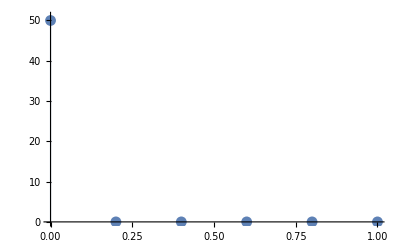

```mathematica
trans[50(*集団人数*),25(*1世代内のペア数*),100(*世代*),2(*恋愛婚成立時の利得*)]
```

```mathematica
trans[50(*集団人数*),5(*1世代内のペア数*),100(*世代*),12(*恋愛婚成立時の利得*)]
```

-Graphics-

class{0.5,0,1,1,0.75,0.5,0,0.5,0.5,0.5,0.75,1,0,0,0.5,0,1,0.5,0,1}

fit{7,11,10,9,7,6}

class{0.75,0,1,1,0.75,0.4375,0.5,0.5,0.75,0.5,0.625,0.25,0.4375,0,0.5,0,0.625,0.625,0,0.75}

fit{13,7,8,10,6,10}

class{0.75,0.3125,0.6875,1,0.75,0.4375,0.625,0.5,0.625,0.75,0.46875,0.25,0.4375,0,0.25,0,0.6875,0.46875,0.25,0.75}

fit{12,4,9,5,6,16}

class{0.875,0.3125,0.6875,0.875,0.75,0.4375,0.53125,0.25,0.3125,0.75,0.46875,0.25,0.53125,0.25,0.25,0.3125,0.6875,0.46875,0.25,0.75}

fit{13,2,10,5,4,14}

class{0.875,0.3125,0.6875,0.875,0.75,0.4375,0.53125,0.46875,0.3125,0.75,0.46875,0.25,0.53125,0.25,0.25,0.3125,0.46875,0.46875,0.25,0.75}

fit{6,0,8,11,0,17}

klist{0.4,1,1,0,0.4,0,0,0.6,0.6,0.6,0.6,0,1,0.6,0.6,0.4,0,0.4,1,0.6}

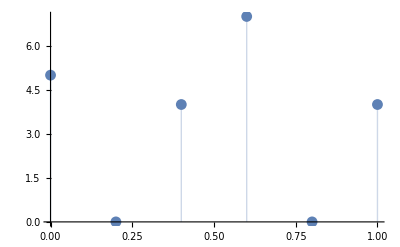

```mathematica
Module[{n=20(*集団人数*),m=20(*ペア個数*),gene=5(*世代*),
v=2(*恋愛婚成立時の利得*),id(*n人分の個体番号*),klist(*　n人分の戦略*),
k0={0,0.2,0.4,0.6,0.8,1}(*適合度計算用*),
class(*n人分の階層スコア*),benefit(*n人分の利得*),pair(*マッチングした番号*),
fit(*核戦略の適合度*)},

(*初期条件の入力 *)
id=Range[n];(* マッチング用個体番号 *)
class=Table[Random[Integer,{0,1}],{n}];(*　階層スコア初期値 Print[class];*)
klist=Table[0.2*Random[Integer,{0,5}],{n}];(*　戦略kの初期値　0--1間を0.2刻み;Print[klist];*)
benefit=Table[0,{n}];(*利得の初期値態 *)

Do[(* ここから1世代内での行動を指定する *)
(*最初に利得benefit，適合度fitを初期化する*)
benefit=Table[0,{n}];(* 利得benefit初期化 *)
fit={0,0,0,0,0,0};(*戦略別適合度fitの初期化*)

Do[(*「pairを一個だけ作る操作」をm回反復してm個のペアを作る．
classはペアを1個作るたびに即時更新される．classは1世代内(gene内)でも更新される *)
pair=RandomSample[id,2];(*　ペアを一つ作る　*)
If[class⟦pair⟦1⟧⟧-class⟦pair⟦2⟧⟧≤klist⟦pair⟦1⟧⟧,(* 相手の階層スコアをチェック *)
benefit⟦pair⟦2⟧⟧=benefit⟦pair⟦2⟧⟧+1;benefit⟦pair⟦1⟧⟧=benefit⟦pair⟦1⟧⟧+1,
(*ここまで見合い婚成立．階層スコア変化無し*)
benefit⟦pair⟦2⟧⟧=benefit⟦pair⟦2⟧⟧+v;benefit⟦pair⟦1⟧⟧=benefit⟦pair⟦1⟧⟧+v;(*  恋愛婚成立，階層スコア更新*)
class⟦pair⟦1⟧⟧=class⟦pair⟦2⟧⟧=(class⟦pair⟦1⟧⟧+class⟦pair⟦2⟧⟧)/2.0]
(* Ifおわり*),{m}];(*m個のマッチング反復終わり ;Print["class",class]; *)
Print["class",class];
(*戦略別に利得を合計して適合度fitに代入*)
Table[Table[If[klist⟦i⟧==k0⟦j⟧,fit⟦j⟧=fit⟦j⟧+benefit⟦i⟧],{j,1,6}],{i,1,n}];
(*  適合度に基づくルーレットセレクション　*)
Print["fit",fit];
klist=Table[RandomChoice[(*weight*)fit->{0,0.2,0.4,0.6,0.8,1}],{i,1,n}],{gene}];
Print["klist",klist];
ListPlot[Transpose[{Table[i,{i,0,1,0.2}],BinCounts[klist,{0,1.2,0.2}]}],Filling->Axis]
(*Histogram[klist,{0.05}(*Binの幅指定*)*)]
```

```mathematica
Module[{n=20(*集団人数*),m=20(*ペア個数*),gene=5(*世代*),
v=2(*恋愛婚成立時の利得*),id(*n人分の個体番号*),klist(*　n人分の戦略*),
k0={0,0.2,0.4,0.6,0.8,1}(*適合度計算用*),
class(*n人分の階層スコア*),benefit(*n人分の利得*),pair(*マッチングした番号*),
fit(*核戦略の適合度*)},

(*初期条件の入力 *)
id=Range[n];(* マッチング用個体番号 *)
class=Table[Random[Integer,{0,1}],{n}];(*　階層スコア初期値 Print[class];*)
klist=Table[0.2*Random[Integer,{0,5}],{n}];(*　戦略kの初期値　0--1間を0.2刻み;Print[klist];*)
benefit=Table[0,{n}];(*利得の初期値態 *)

Do[(* ここから1世代内での行動を指定する *)
(*最初に利得benefit，適合度fitを初期化する*)
benefit=Table[0,{n}];(* 利得benefit初期化 *)
fit={0,0,0,0,0,0};(*戦略別適合度fitの初期化*)

Do[(*「pairを一個だけ作る操作」をm回反復してm個のペアを作る．
classはペアを1個作るたびに即時更新される．classは1世代内(gene内)でも更新される *)
pair=RandomSample[id,2];(*　ペアを一つ作る　*)
If[class⟦pair⟦1⟧⟧-class⟦pair⟦2⟧⟧≤klist⟦pair⟦1⟧⟧,(* 相手の階層スコアをチェック *)
benefit⟦pair⟦2⟧⟧=benefit⟦pair⟦2⟧⟧+1;benefit⟦pair⟦1⟧⟧=benefit⟦pair⟦1⟧⟧+1,
(*ここまで見合い婚成立．階層スコア変化無し*)
benefit⟦pair⟦2⟧⟧=benefit⟦pair⟦2⟧⟧+v;benefit⟦pair⟦1⟧⟧=benefit⟦pair⟦1⟧⟧+v;(*  恋愛婚成立，階層スコア更新*)
class⟦pair⟦1⟧⟧=(class⟦pair⟦1⟧⟧+class⟦pair⟦2⟧⟧)/2;class⟦pair⟦2⟧⟧=(class⟦pair⟦1⟧⟧+class⟦pair⟦2⟧⟧)]
(* Ifおわり*),{m}];(*m個のマッチング反復終わり ;Print["class",class]; *)
Print["class",class];
(*戦略別に利得を合計して適合度fitに代入*)
Table[Table[If[klist⟦i⟧==k0⟦j⟧,fit⟦j⟧=fit⟦j⟧+benefit⟦i⟧],{j,1,6}],{i,1,n}];
(*  適合度に基づくルーレットセレクション　*)
Print["fit",fit];
klist=Table[RandomChoice[(*weight*)fit->{0,0.2,0.4,0.6,0.8,1}],{i,1,n}],{gene}];
Print["klist",klist];
Print[BinCounts[klist,{0,1.2,0.2}]];(* 最終的な戦略kの分布 *)



ListPlot[Table[{i,Count[klist,i]},{i,0,1,0.2}],PlotRange->{0,110},
Filling->Axis,PlotStyle->PointSize[Large]]
]
```

class{5/4,1/2,1,1/2,1/2,1,1,0,1/2,0,0,1/2,0,1,0,0,3/4,0,0,1}

fit{15,5,2,9,8,9}

class{5/4,1/2,1,1/2,1/2,1,1,0,1/2,0,0,1/2,0,1,0,0,3/4,0,0,1}

fit{17,0,0,8,7,8}

class{5/4,19/16,1,1/2,1/2,1,1/2,1/2,1/2,0,0,1/2,0,11/16,0,0,21/16,0,0,37/16}

fit{24,0,0,12,6,6}

class{31/32,19/16,1,165/128,101/128,1,1/2,1/2,49/32,1/4,0,1/2,53/64,53/64,0,0,21/32,0,37/64,41/32}

fit{36,0,0,18,0,0}

class{273/512,19/16,1,303/512,101/128,1,1273/512,1/2,49/32,401/512,451/512,357/256,53/64,1013/1024,0,0,1685/1024,0,37/128,41/32}

fit{40,0,0,16,0,0}

klist{0,0.6,0,0.6,0.6,0,0.6,0.6,0,0,0,0,0,0.6,0,0,0.6,0,0,0.6}

{12,0,0,8,0,0}

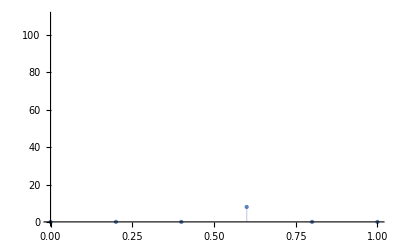

```mathematica
ListPlot[{Table[i,{i,0,1,0.2}],BinCounts[klist,{0,1.2,0.2}]}]
```

```mathematica
klist=Table[RandomChoice[(*weight*)fit->{0,0.2,0.4,0.6,0.8,1.0}],{i,1,n}],{gene}];
(*世代geneの反復Do おわり*)
```

```mathematica
Length[{0.8,0.8,0.4,0.4,0.8,0,0.8,0.8,1.,0.4,1.,0.8,0,1.,1.,0.8,1.,0,0.8,0,0.4,0.8,1.,0.4,0.8,0.4,0.8,0.4,1.,0,0,0,0.8,1.,1.,0.8,1.,0,0.8,0.8,0,0.8,0,1.,0.8,0.8,0.8,0.8,0.8,0.8}]
```

50

```mathematica
"klist"{0.8,0.8,0.4,0.4,0.8,0,0.8,0.8,1.,0.4,1.,0.8,0,1.,1.,0.8,1.,0,0.8,0,0.4,0.8,1.,0.4,0.8,0.4,0.8,0.4,1.,0,0,0,0.8,1.,1.,0.8,1.,0,0.8,0.8,0,0.8,0,1.,0.8,0.8,0.8,0.8,0.8,0.8}
```

```mathematica
klist=Table[RandomChoice[(*weight*)fit->{0,0.2,0.4,0.6,0.8,1.0}],{i,1,n}],{gene}];
(*世代geneの反復Do おわり*)
Print[Table[Count[klist,i],{i,0,1,0.2}]];(* 最終的な戦略kの分布 *)
ListPlot[Table[{i,Count[klist,i]},{i,0,1,0.2}],PlotRange->{0,110},
Filling->Axis,PlotStyle->PointSize[Large]]
```

```mathematica
Module[{klist,n=10,benefit,fit},
klist=Table[Random[Integer,{-5,6}],{n}];
benefit=Table[Random[Integer,{0,10}],{n}];
Print[klist];
Print[benefit];
fit=Table[0,{12}];(*戦略別適合度*)
Table[
Table[
If[klist⟦i⟧==(j-6),fit⟦j⟧=fit⟦j⟧+benefit⟦i⟧],{j,1,12}],{i,1,n}];
fit]
```

{1,2,-3,-2,2,0,4,-2,4,2}

{9,3,4,5,3,3,3,7,0,3}

{0,0,4,12,0,3,9,9,0,3,0,0}

```mathematica
Table[0.2*Random[Integer,{0,5}],{100}]
```

{0.2,0.4,0.2,0.2,0.4,0.4,0.4,1.,1.,0.8,0.4,0.6,0.6,0.8,1.,1.,0.8,0.4,0.,0.,0.,0.8,1.,0.2,0.2,0.6,1.,0.,0.4,0.4,0.6,1.,0.4,0.,1.,1.,0.8,0.6,0.,0.8,0.2,0.,0.8,0.4,0.4,0.,1.,0.2,0.6,0.6,1.,0.8,1.,0.,0.4,0.4,0.8,0.6,0.2,1.,1.,0.4,0.,0.4,0.4,0.6,1.,0.6,1.,0.,1.,1.,0.6,0.,0.8,0.,0.6,0.2,0.,0.6,0.8,0.2,1.,0.8,0.4,0.4,0.8,0.8,0.6,0.6,1.,0.,0.2,0.4,0.2,0.4,0.2,0.,0.6,0.4}

```mathematica
If[0.2>Random[],1,0]
```

0

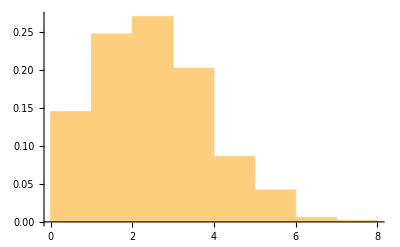

```mathematica
Histogram[Table[Total[Table[If[0.1>Random[],1,0],{20}]],{1000}],Automatic,"Probability"]
```

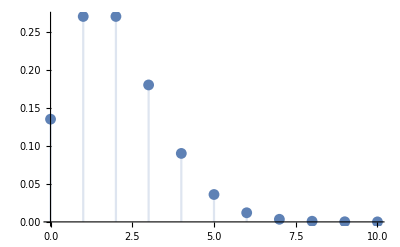

```mathematica
DiscretePlot[PDF[PoissonDistribution[2],x],{x,0,10}]
```

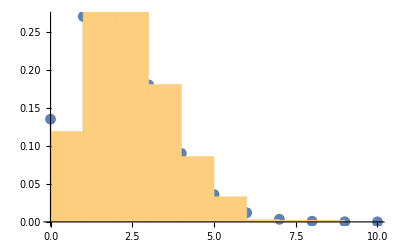

```mathematica
Show[DiscretePlot[PDF[PoissonDistribution[2],x],{x,0,10}],Histogram[Table[Total[Table[If[0.1>Random[],1,0],{20}]],{1000}],Automatic,"Probability"]]
```